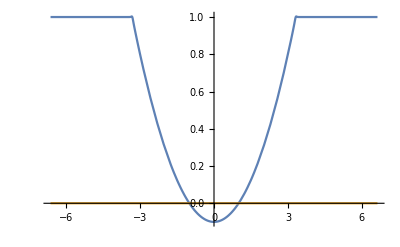

```mathematica
(*Configuration*)
a=0.1;
ν=0.0000001;
n=100.;

b=(1.+1./a)^(-n);
Epsilon = Function[x,1.+(a*(x^2.-1.)+ⅈ*ν-1.)/(1.+b*x^(2.n))];

X0=2.*Sqrt[1.+1./a];
Plot[{Re[Epsilon[x]],Im[Epsilon[x]]},{x,-X0,X0},PlotRange->Full]

A=1.;
```

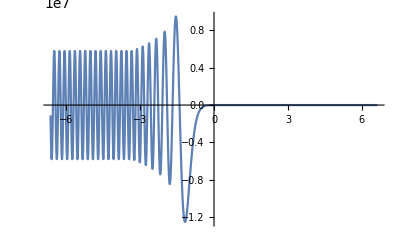

0.0000356109

```mathematica
(*TE-wave*)
ETEEquation={y''[x]+χ^2.*(Epsilon[x]-Sin[θ]^2.)*y[x]==0.};
ETEInitials={y[X0]==A,y'[X0]==ⅈ*χ*A} (* χ=k0*L, where L is a width of the layer *);

ETE=ParametricNDSolveValue[{ETEEquation,ETEInitials},y,{x,-X0,X0},{θ,χ}];
Plot[Re[ETE[0.,30.][x]],{x,-X0,X0},PlotRange->Full]

RTE=Function[{θ,χ},Exp[2.*ⅈ*χ*(-X0)]*(ⅈ*χ*ETE[θ,χ][-X0]-ETE[θ,χ]'[-X0])/(ⅈ*χ*ETE[θ,χ][-X0]+ETE[θ,χ]'[-X0])];
TTE=Function[{θ,χ},ETE[θ,χ][X0]*Exp[-ⅈ*χ*(X0)]*(Exp[ⅈ*χ*(-X0)]+RTE[θ,χ]*Exp[-ⅈ*χ*(-X0)])/ETE[θ,χ][-X0]];

TEDissipation =Function[{θ,χ},1. - Abs[RTE[θ,χ]]^2.-Abs[TTE[θ,χ]]^2.];
TEDissipation[0.,30.]
```

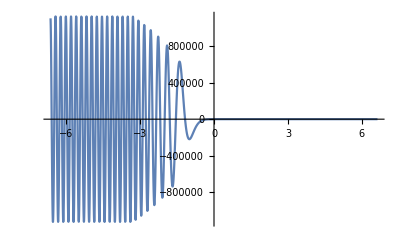

0.0000355848

```mathematica
(*TM-wave*)
BTMEquation={y''[x]-(Epsilon'[x]/Epsilon[x])*y'[x]+χ^2.*(Epsilon[x]-Sin[θ]^2.)*y[x]==0};
BTMInitials={y[X0]==-A,y'[X0]==-ⅈ*χ*Epsilon[X0]*A*Cos[θ]};

BTM=ParametricNDSolveValue[{BTMEquation,BTMInitials},y,{x,-X0,X0},{θ,χ}];
Plot[Re[BTM[0.,30.][x]],{x,-X0,X0},PlotRange->Full]

RTM=Function[{θ,χ},Exp[2.*ⅈ*χ*(-X0)]*(ⅈ*χ*BTM[θ,χ][-X0]-BTM[θ,χ]'[-X0])/(ⅈ*χ*BTM[θ,χ][-X0]+BTM[θ,χ]'[-X0])];
TTM=Function[{θ,χ},BTM[θ,χ][X0]*Exp[-ⅈ*χ*(X0)]*(Exp[ⅈ*χ*(-X0)]+RTM[θ,χ]*Exp[-ⅈ*χ*(-X0)])/BTM[θ,χ][-X0]];

TMDissipation=Function[{θ,χ},1.-Abs[RTM[θ,χ]]^2.-Abs[TTM[θ,χ]]^2.];
TMDissipation[0.,30.]
```

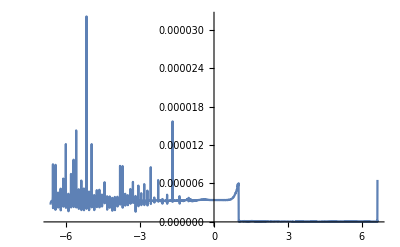

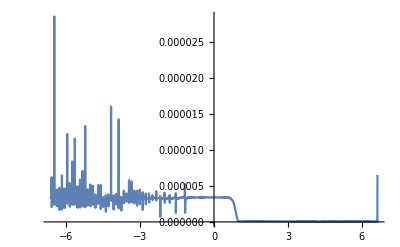

```mathematica
(*Reletive precision*)
values={θ->0.,χ->30.};
ETM=Function[x,ⅈ*BTM[θ,χ]'[x]/(χ*Epsilon[x])];
Plot[Abs[ETE[θ,χ][x]-ETM[x]]/Min[Abs[ETE[θ,χ][x]],Abs[ETM[x]]]/.values,{x,-X0,X0},PlotRange->Full]

BTE=Function[x,(-ⅈ/χ)*ETE[θ,χ]'[x]];
Plot[Abs[BTE[x]+BTM[θ,χ][x]]/Min[Abs[BTE[x]],Abs[BTM[θ,χ][x]]]/.values,{x,-X0,X0},PlotRange->Full]
```

```mathematica
limits={χ1->5.,χ2->50.};
Teta=Function[χ,Abs[θ/.NMaximize[TMDissipation[θ,χ],θ][[2]]]];
Data=Table[Teta[x],{x,χ1/.limits,χ2/.limits}];
```

{m→-0.347467,h→0.424015}

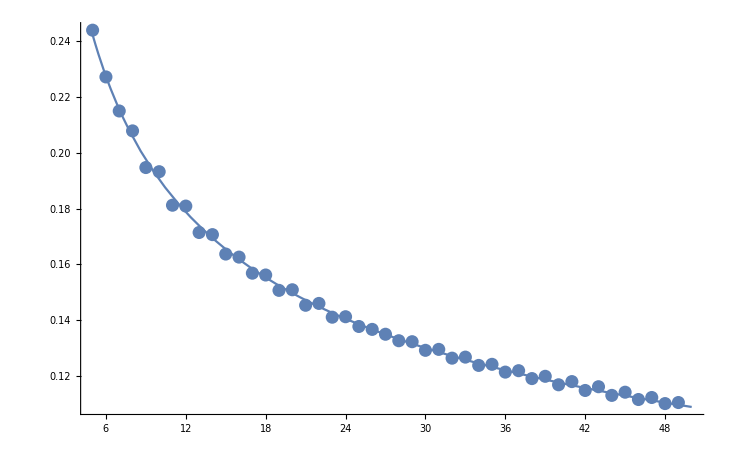

```mathematica
points=Table[Prepend[{Data[[i]]},i+(χ1-1)/.limits],{i,(χ2-χ1)/.limits}];
fit=FindFit[points,h*x^m,{m,h},x]
Experiment=ListPlot[points];
Approximation=Plot[(h*x^m)/.fit,{x,χ1/.limits,χ2/.limits}];
Show[Experiment,Approximation,PlotRange->Automatic]
```

```mathematica
(*Anisotropy*)
V = Function[x, 1. - Epsilon[x]];
U = 0.(*10.^(-20) ( U = (eB/(mcw))^2, so for B~1000G U~10^(-20) *);
Px = Function[x, 1. - V[x]/(1. + U^(1./2.))] (*P for Permittivity*);
Py = Function[x, 1. - V[x]/(1. - U^(1./2.))];
Pz = Function[x, 1. - V[x]] (*Magnetic field direction*); 

GeneralSystem = {
(*Ex[x]*Px[x]==Cos[ϕ]*By[x]-Sin[θ]*Bz[x], (*usually ϕ=π/2, it's angle between k and z; θ is between k and x*)
Bx[x] == Ez[x]*Sin[θ] -Ey[x] * Cos[ϕ],*)
Ey'[x]==ⅈ*χ*(Sin[θ]*(Cos[ϕ]*By[x]-Sin[θ]*Bz[x])/Px[x]+Bz[x]),(*Ey'[x]==ⅈ*χ*(Sin[θ]*Ex[x]+Bz[x])*)
Ez'[x]==ⅈ*χ*(Cos[ϕ]*(Cos[ϕ]*By[x]-Sin[θ]*Bz[x])/Px[x]-By[x]),(*Ez'[x]==ⅈ*χ*(Cos[ϕ]*Ex[x]-By[x])*)
By'[x]==ⅈ*χ*(Sin[θ]*(Ez[x]*Sin[θ] -Ey[x] * Cos[ϕ])-Pz[x]*Ez[x]),(*By'[x]==ⅈ*χ*(Sin[θ]*Bx[x]-Pz[x]*Ez[x])*)
Bz'[x]==ⅈ*χ*(Cos[ϕ]*(Ez[x]*Sin[θ] -Ey[x] * Cos[ϕ])+Py[x]*Ey[x])(*Bz'[x]==ⅈ*χ*(Cos[ϕ]*Bx[x]+Py[x]*Ey[x])*)
};

GeneralInitials = { 
(*Ex[X0]==A*(Sin[θ]Sin[α]-Cos[ϕ]Cos[θ]Cos[α]),*)
Ey[X0]==-A*(Cos[θ]Sin[α]+Cos[ϕ]Sin[θ]Cos[α]),
Ez[X0]==A*Sin[ϕ]Cos[α],
(*Bx[X0]==A*(Sin[θ]Cos[α]+Cos[ϕ]Cos[θ]Sin[α]),*)
By[X0]==A*(Cos[ϕ]Sin[θ]Sin[α]-Cos[θ]Cos[α]),
Bz[X0]==-A*Sin[ϕ]Sin[α]
};

Solution = NDSolveValue[{GeneralSystem,GeneralInitials}/.{χ->30.,θ->0.,ϕ->π/2.,α->0.},{Ey,Ez,By,Bz},{x,-X0,X0}];

Eτ=Function[x,If[Solution[[1]][X0]==0,Solution[[2]][x],Solution[[1]][x]/Cos[ArcTan[Abs[Solution[[2]][X0]]/Abs[Solution[[1]][X0]]]]]];
Plot[Re[Eτ[x]],{x,-X0,X0}]

R=Function[χ,Exp[2.*ⅈ*χ*(-X0)]*(ⅈ*χ*Eτ[-X0]-Eτ'[-X0])/(ⅈ*χ*Eτ[-X0]+Eτ'[-X0])];
T=Function[χ,Eτ[X0]*Exp[-ⅈ*χ*(X0)]*(Exp[ⅈ*χ*(-X0)]+R[χ]*Exp[-ⅈ*χ*(-X0)])/Eτ[-X0]];
Dissipation = Function[χ,1. - Abs[R[χ]]^2.-Abs[T[χ]^2.]];

Dissipation[30]
```

-Graphics-

0.0000356109

```mathematica
ClearAll[T,v];
T={{ⅈ,-ⅈ,0},{1,1,0},{0,0,1}};
DispDet = {{1-v/(1+u)-(x^2+y^2+z^2),0,0},{0,1-v/(1-u)-(x^2+y^2+z^2),0},{0,0,1-v-(x^2+y^2+z^2)}}+Inverse[T].{{x^2,x*y,x*z},{x*y,y^2,y*z},{x*z,y*z,z^2}}.T;
MatrixForm[T.{{1-v/(1+u),0,0},{0,1-v/(1-u),0},{0,0,1-v}}.Inverse[T]]
MatrixForm[DispDet]
```

(1/2 (1-v/(1-u))+1/2 (1-v/(1+u)) | -1/2 ⅈ (1-v/(1-u))+1/2 ⅈ (1-v/(1+u)) | 0
1/2 ⅈ (1-v/(1-u))-1/2 ⅈ (1-v/(1+u)) | 1/2 (1-v/(1-u))+1/2 (1-v/(1+u)) | 0
0 | 0 | 1-v)

(1-v/(1+u)-x^2-(ⅈ x y)/2-y^2/2+ⅈ (-(ⅈ x^2)/2+(x y)/2)-z^2 | -1/2 ⅈ x y+y^2/2-ⅈ (-(ⅈ x^2)/2+(x y)/2) | -1/2 ⅈ x z+(y z)/2
(ⅈ x y)/2+y^2/2+ⅈ ((ⅈ x^2)/2+(x y)/2) | 1-v/(1-u)-x^2+(ⅈ x y)/2-y^2/2-ⅈ ((ⅈ x^2)/2+(x y)/2)-z^2 | (ⅈ x z)/2+(y z)/2
ⅈ x z+y z | -ⅈ x z+y z | 1-v-x^2-y^2)

```mathematica
Simplify[Det[DispDet]]/.{x^2+y^2+z^2->k^2}
```

((-1+v) (-1+k^2+v)^2+(-1+k^2) u^2 (-1+k^2+v-v z^2))/(-1+u^2)

```mathematica
Simplify[(2(v-1)^2+u(v(1-z^2)-2))^2-4*(v+u-1)*((v-1)^3-u(v(1-z^2)-1))]
```

u v^2 (-4 (-1+v) z^2+u (-1+z^2)^2)

```mathematica
Plot[Im[ETM[1]*Conjugate[Sin[θ]BTM[θ,χ][1]/Epsilon[1]]]/.{θ->x,χ->30},{x,-π/2,π/2}]
```

-Graphics-